## Common

```mathematica
Needs["PlotLegends`"]
```

```mathematica
readRunFitness[name_]:=
Module[{allData,noHeaderData,data},
allData = ImportString[Import[name],"TSV"];
noHeaderData = Rest[allData];
data = noHeaderData⟦All,2;;⟧;
{data,noHeaderData⟦All,1⟧, Mean[Transpose[data]], Median[Transpose[data]], Min/@data}
]
```

```mathematica
readRunEvaluationInfo[name_]:=
Module[{allData,noHeaderData,data},
allData = ImportString[Import[name],"TSV"];
data = Rest[allData];
{data,Max/@data, Mean[Transpose[data]], Median[Transpose[data]], Min/@data}
]
```

```mathematica
enlarge[list_, fill_, stat_]:=list~Join~Array[fill&,Max[Length/@stat]-Length[list]]
```

```mathematica
enlarge[list_, fill_, stat_, len_]:=list~Join~Array[fill&,len-Length[list]]
```

This function reads single stat for all experiment runs by multiple parameters/methods. Typical use for "experiments_???.txt" file.

```mathematica
readFinalStats[names_List,statName_]:=
Module[{allData},
allData = ImportString[Import[#],"TSV"]&/@names;
allData⟦#⟦1⟧,2;;,#⟦3⟧⟧&/@Position[allData,statName]
]
```

Reads all stat names from multiple parameters/methods. Returns their intersection.

```mathematica
readFinalStatNames[names_List]:=
Module[{allData},
Flatten[Intersection[(ImportString[Import[#],"TSV"]&/@names)⟦All,1,All⟧]]
]
```

```mathematica
listAllExperimentFiles[dirs_List]:=
Flatten[FileNames[RegularExpression["experiments\\_\\d\\d\\d\\.txt"],{"/Users/drchaj1/java/exp/"<>#}]&/@dirs]
```

## Fitness of a Single Run

```mathematica
{data, bsf, avg, med, min}=readRunFitness["~/java/exp/results/run_001_001_FITNESS.txt"];
```

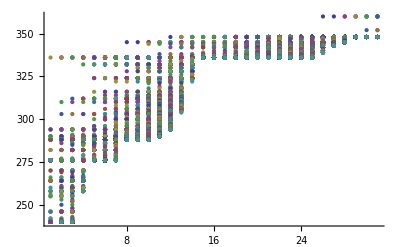

```mathematica
ListPlot[Transpose[data], PlotRange->All]
```

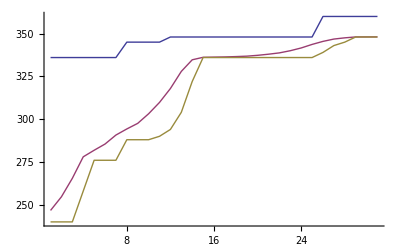

```mathematica
ListLinePlot[{bsf, avg, min}, PlotRange->All]
```

## Fitness over Multiple Runs

```mathematica
bsfAvg = (readRunFitness[#]⟦2⟧&/@FileNames["run_001*FITNESS.txt",{"~/java/exp/results"}]);
```

```mathematica
Max[Length[#]&/@bsfAvg]
```

161

```mathematica
enlarge[list_]:=list~Join~Array[Max[bsfAvg]&,Max[Length/@bsfAvg]-Length[list]]
```

```mathematica
bsfAvg=Mean[(enlarge/@bsfAvg)];
```

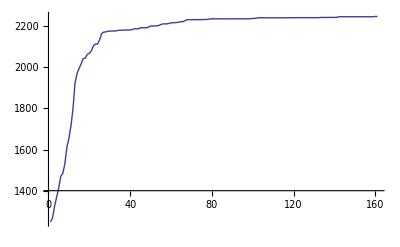

```mathematica
ListLinePlot[{bsfAvg}, PlotRange->All]
```

## Evaluation of a Single Run

```mathematica
{data, max, avg, med, min}=readRunEvaluationInfo["~/java/exp/results/run_001_001_AVG_DISTANCE.txt"];
```

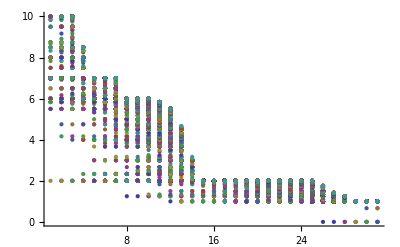

```mathematica
ListPlot[Transpose[data], PlotRange->All]
```

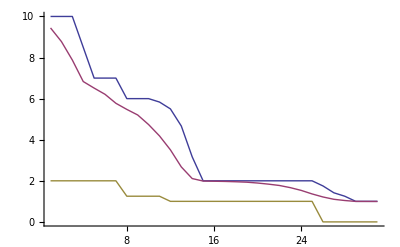

```mathematica
ListLinePlot[{max, avg, min}, PlotRange->All]
```

## Evaluation over Multiple Runs

```mathematica
bsfAvg = (readRunEvaluationInfo[#]⟦5⟧&/@FileNames["run_001*AVG_DISTANCE.txt",{"~/java/exp/results"}]);
```

```mathematica
Max[Length[#]&/@bsfAvg]
```

161

```mathematica
bsfAvg=Mean[enlarge[#,Min[bsfAvg], bsfAvg]&/@bsfAvg];
```

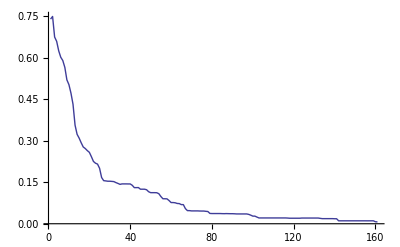

```mathematica
ListLinePlot[{bsfAvg}, PlotRange->All]
```

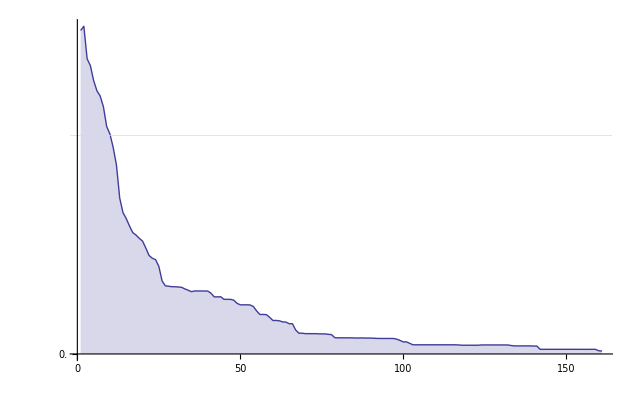

```mathematica
Show[ListLinePlot[{bsfAvg[[1;;]]}, PlotRange->All, Ticks->{Range[0,300, 50],Range[0,25, 0.5]},Filling->Axis,AxesOrigin->{0,0}], GridLines->{None, {0.5}}]
```

## Evaluation over Multiple Methods

```mathematica
singleMethod[methodDir_, variable_, column_] :=
Module[{stat},
stat=(readRunFitness[#]⟦column⟧&/@(Complement[FileNames["run_001*"<>variable<>".txt",{"~/java/exp/results/"<>methodDir}],FileNames["run_001*GENERALIZATION*.txt",{"~/java/exp/results/"<>methodDir}]]));
Mean[enlarge[#,Max[#], stat]&/@stat]
]
```

```mathematica
singleMethodGeneralization[methodDir_, variable_] :=
Module[{stat},
stat = Sequence@@Flatten[#,{3}]&@(ImportString[Import[#],"TSV"]&/@
Intersection[FileNames["run_001*"<>variable<>".txt",{"~/java/exp/results/"<>methodDir}],FileNames["run_001*GENERALIZATION*.txt",{"~/java/exp/results/"<>methodDir}]]);
Mean[enlarge[#,Min[#], stat]&/@stat]
]
```

```mathematica
singleMethodDiversity[methodDir_, variable_] :=
Module[{stat},
stat = Sequence@@Flatten[#,{3}]&@(ImportString[Import[#],"TSV"]&/@
FileNames["run_001_*"<>variable<>"*.txt",{"~/java/exp/results/"<>methodDir}]);
Rescale[Mean[enlarge[#,Mean[#], stat]&/@stat]];
Mean[enlarge[#,Mean[#], stat]&/@stat]
]
```

```mathematica
multipleMethods[methodDirs_, variable_, column_, generalization_:True] :=
Module[{stats, len},
If[generalization==True,
stats=(singleMethod[#,variable, column]&/@methodDirs)~Join~(singleMethodGeneralization[#,variable]&/@methodDirs),
stats=(singleMethod[#,variable, column]&/@methodDirs)];
len = Max[Length/@stats];
stats=enlarge[#,Min[#], stats, len]&/@stats;
Show[
ListLinePlot[stats, PlotRange->All, Ticks->{Range[0,300, 50],Range[0,25, 0.5]},AxesOrigin->{0,0}, PlotStyle->{Thickness[0.005]},
PlotLegend->methodDirs~Join~(StringJoin[#," G"]&/@methodDirs),
PlotMarkers->Automatic,
LegendPosition->{1.1,-0.4}
], 
GridLines->{None, {0.5}}]
]
```

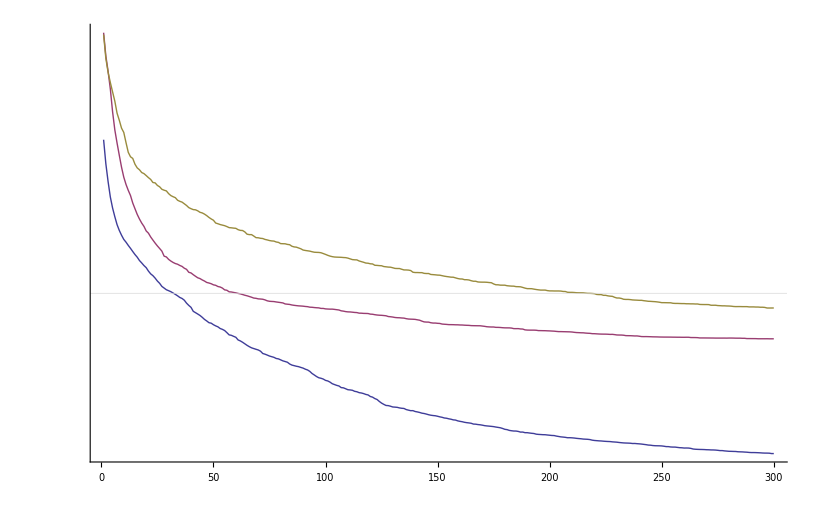

```mathematica
multipleMethods[{"FC_NEAT", "FC_GP", "FC_GPDC"}, "AVG_DISTANCE", 5]
```

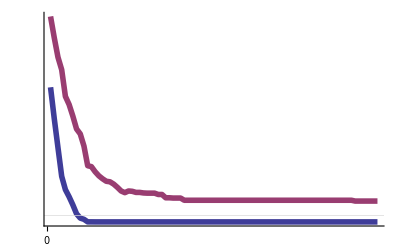

```mathematica
multipleMethods[{"T_NEAT", "T_GP"}, "AVG_DISTANCE", 5]
```

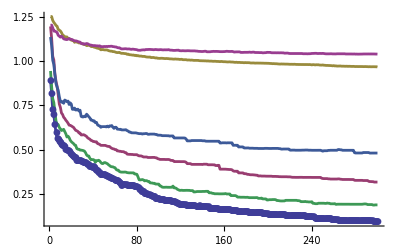

```mathematica
multipleMethods[{"FC_NEAT_7_20", "FC_GP_7_20", "FC_SADE_7_20"}, "AVG_DISTANCE", 5]
```

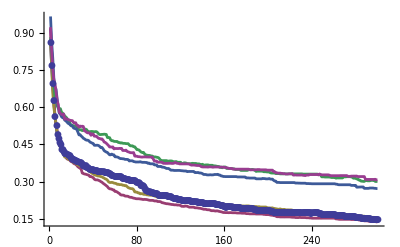

```mathematica
multipleMethods[{"DIV_GP_5_50", "DIV_NEAT_5_50", "DIV_NEAT_5_50_AMP10"}, "AVG_DISTANCE", 5]
```

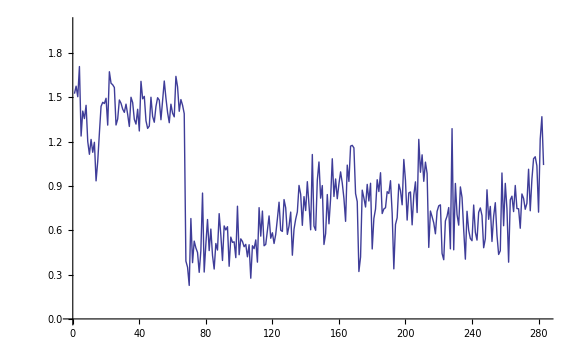

```mathematica
ListLinePlot[singleMethodDiversity[{"DIV_GP_5_50"},"DIVERSITY"],PlotRange->{0,2}]
```

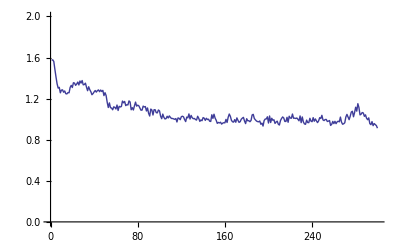

```mathematica
ListLinePlot[singleMethodDiversity[{"DIV_NEAT_5_50"},"DIVERSITY"],PlotRange->{0,2}]
```

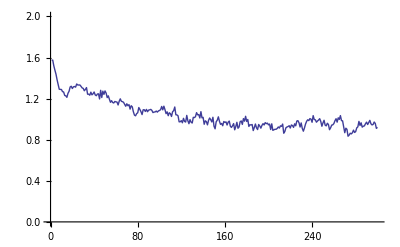

```mathematica
ListLinePlot[singleMethodDiversity[{"DIV_NEAT_5_50_AMP10"},"DIVERSITY"],PlotRange->{0,2}]
```

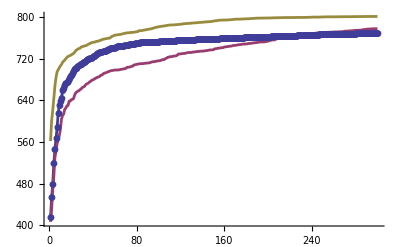

```mathematica
multipleMethods[{"DIV_GP_7_50","DIV_GPC_7_50", "DIV_NEAT_7_50"}, "FITNESS", 2, False]
```

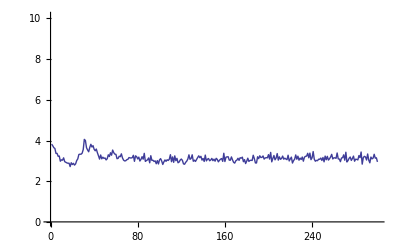

```mathematica
ListLinePlot[singleMethodDiversity[{"DIV_GP_7_50"},"P_DIVERSITY"],PlotRange->{0,10.1}]
```

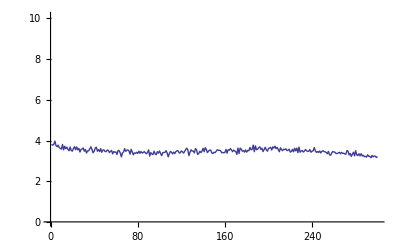

```mathematica
ListLinePlot[singleMethodDiversity[{"DIV_GPC_7_50"},"P_DIVERSITY"],PlotRange->{0,10.1}]
```

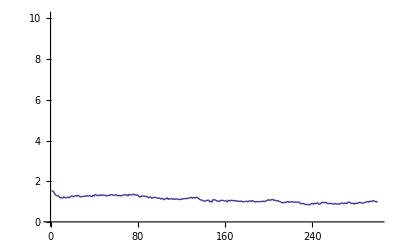

```mathematica
ListLinePlot[singleMethodDiversity[{"DIV_NEAT_7_50"},"P_DIVERSITY"],PlotRange->{0,10.1}]
```

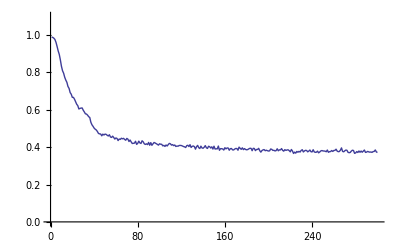

```mathematica
ListLinePlot[singleMethodDiversity[{"DIV_GP_7_50"},"G_DIVERSITY"],PlotRange->{0,1.1}]
```

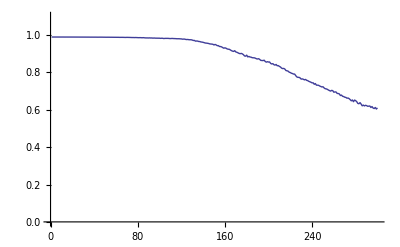

```mathematica
ListLinePlot[singleMethodDiversity[{"DIV_GPC_7_50"},"G_DIVERSITY"],PlotRange->{0,1.1}]
```

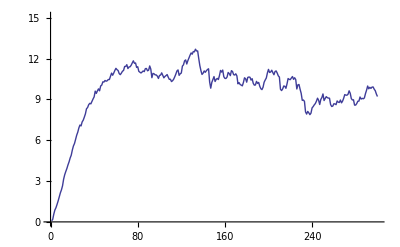

```mathematica
ListLinePlot[singleMethodDiversity[{"DIV_NEAT_7_50"},"G_DIVERSITY"],PlotRange->{0,15.1}]
```

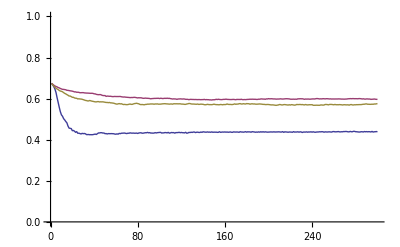

```mathematica
ListLinePlot[{singleMethodDiversity[{"GEP_TOURNAMENT"},"G_DIVERSITY"], singleMethodDiversity[{"GEP_ROULETTE"},"G_DIVERSITY"], singleMethodDiversity[{"GEP_TOURNAMENT2"},"G_DIVERSITY"]},PlotRange->{0,1}]
```

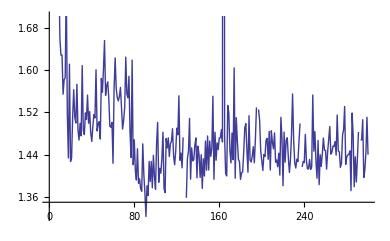

```mathematica
ListLinePlot[{singleMethodDiversity[{"GEP_TOURNAMENT"},"P_DIVERSITY"]}]
```

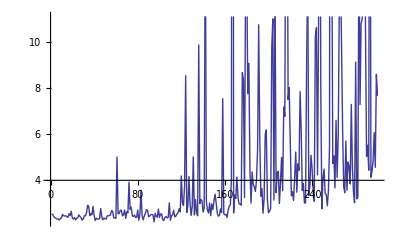

```mathematica
ListLinePlot[{singleMethodDiversity[{"GEP_TOURNAMENT2"},"P_DIVERSITY"]}]
```

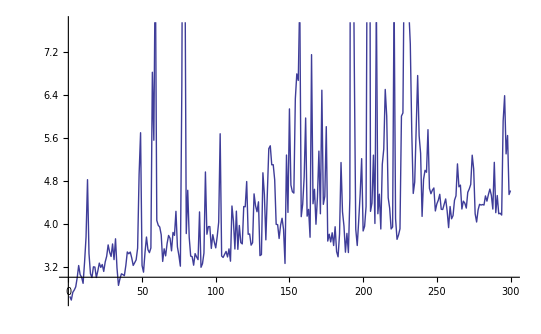

```mathematica
ListLinePlot[{singleMethodDiversity[{"GEP_ROULETTE"},"P_DIVERSITY"]}]
```

## Final Stats

```mathematica
numOfConfs=8;
```

```mathematica
labels=Flatten[Outer[StringJoin,{"GP_","70_","33_","53_","35_","55_"},{"A","B","C","D","E","F","G","H","I","J","K"}]]
```

{GP_A,GP_B,GP_C,GP_D,GP_E,GP_F,GP_G,GP_H,GP_I,GP_J,GP_K,70_A,70_B,70_C,70_D,70_E,70_F,70_G,70_H,70_I,70_J,70_K,33_A,33_B,33_C,33_D,33_E,33_F,33_G,33_H,33_I,33_J,33_K,53_A,53_B,53_C,53_D,53_E,53_F,53_G,53_H,53_I,53_J,53_K,35_A,35_B,35_C,35_D,35_E,35_F,35_G,35_H,35_I,35_J,35_K,55_A,55_B,55_C,55_D,55_E,55_F,55_G,55_H,55_I,55_J,55_K}

```mathematica
labels=Flatten[Outer[StringJoin,{"0",".001",".005",".01",".05",".1",".2",".5"},{"A","B","C","D","E","F","G","H","I","J","K"}]]
```

{0A,0B,0C,0D,0E,0F,0G,0H,0I,0J,0K,.001A,.001B,.001C,.001D,.001E,.001F,.001G,.001H,.001I,.001J,.001K,.005A,.005B,.005C,.005D,.005E,.005F,.005G,.005H,.005I,.005J,.005K,.01A,.01B,.01C,.01D,.01E,.01F,.01G,.01H,.01I,.01J,.01K,.05A,.05B,.05C,.05D,.05E,.05F,.05G,.05H,.05I,.05J,.05K,.1A,.1B,.1C,.1D,.1E,.1F,.1G,.1H,.1I,.1J,.1K,.2A,.2B,.2C,.2D,.2E,.2F,.2G,.2H,.2I,.2J,.2K,.5A,.5B,.5C,.5D,.5E,.5F,.5G,.5H,.5I,.5J,.5K}

```mathematica
files= listAllExperimentFiles[{"GP2D_SL_1000","GPAT2D_SL_70_1000","GPAT2D_SL_1000"}]
```

{/Users/drchaj1/java/exp/GP2D_SL_1000/experiments_001.txt,/Users/drchaj1/java/exp/GP2D_SL_1000/experiments_002.txt,/Users/drchaj1/java/exp/GP2D_SL_1000/experiments_003.txt,/Users/drchaj1/java/exp/GP2D_SL_1000/experiments_004.txt,/Users/drchaj1/java/exp/GP2D_SL_1000/experiments_005.txt,/Users/drchaj1/java/exp/GP2D_SL_1000/experiments_006.txt,/Users/drchaj1/java/exp/GP2D_SL_1000/experiments_007.txt,/Users/drchaj1/java/exp/GP2D_SL_1000/experiments_008.txt,/Users/drchaj1/java/exp/GP2D_SL_1000/experiments_009.txt,/Users/drchaj1/java/exp/GP2D_SL_1000/experiments_010.txt,/Users/drchaj1/java/exp/GP2D_SL_1000/experiments_011.txt,/Users/drchaj1/java/exp/GPAT2D_SL_70_1000/experiments_001.txt,/Users/drchaj1/java/exp/GPAT2D_SL_70_1000/experiments_002.txt,/Users/drchaj1/java/exp/GPAT2D_SL_70_1000/experiments_003.txt,/Users/drchaj1/java/exp/GPAT2D_SL_70_1000/experiments_004.txt,/Users/drchaj1/java/exp/GPAT2D_SL_70_1000/experiments_005.txt,/Users/drchaj1/java/exp/GPAT2D_SL_70_1000/experiments_006.txt,/Users/drchaj1/java/exp/GPAT2D_SL_70_1000/experiments_007.txt,/Users/drchaj1/java/exp/GPAT2D_SL_70_1000/experiments_008.txt,/Users/drchaj1/java/exp/GPAT2D_SL_70_1000/experiments_009.txt,/Users/drchaj1/java/exp/GPAT2D_SL_70_1000/experiments_010.txt,/Users/drchaj1/java/exp/GPAT2D_SL_70_1000/experiments_011.txt,/Users/drchaj1/java/exp/GPAT2D_SL_1000/experiments_001.txt,/Users/drchaj1/java/exp/GPAT2D_SL_1000/experiments_002.txt,/Users/drchaj1/java/exp/GPAT2D_SL_1000/experiments_003.txt,/Users/drchaj1/java/exp/GPAT2D_SL_1000/experiments_004.txt,/Users/drchaj1/java/exp/GPAT2D_SL_1000/experiments_005.txt,/Users/drchaj1/java/exp/GPAT2D_SL_1000/experiments_006.txt,/Users/drchaj1/java/exp/GPAT2D_SL_1000/experiments_007.txt,/Users/drchaj1/java/exp/GPAT2D_SL_1000/experiments_008.txt,/Users/drchaj1/java/exp/GPAT2D_SL_1000/experiments_009.txt,/Users/drchaj1/java/exp/GPAT2D_SL_1000/experiments_010.txt,/Users/drchaj1/java/exp/GPAT2D_SL_1000/experiments_011.txt,/Users/drchaj1/java/exp/GPAT2D_SL_1000/experiments_012.txt,/Users/drchaj1/java/exp/GPAT2D_SL_1000/experiments_013.txt,/Users/drchaj1/java/exp/GPAT2D_SL_1000/experiments_014.txt,/Users/drchaj1/java/exp/GPAT2D_SL_1000/experiments_015.txt,/Users/drchaj1/java/exp/GPAT2D_SL_1000/experiments_016.txt,/Users/drchaj1/java/exp/GPAT2D_SL_1000/experiments_017.txt,/Users/drchaj1/java/exp/GPAT2D_SL_1000/experiments_018.txt,/Users/drchaj1/java/exp/GPAT2D_SL_1000/experiments_019.txt,/Users/drchaj1/java/exp/GPAT2D_SL_1000/experiments_020.txt,/Users/drchaj1/java/exp/GPAT2D_SL_1000/experiments_021.txt,/Users/drchaj1/java/exp/GPAT2D_SL_1000/experiments_022.txt,/Users/drchaj1/java/exp/GPAT2D_SL_1000/experiments_023.txt,/Users/drchaj1/java/exp/GPAT2D_SL_1000/experiments_024.txt,/Users/drchaj1/java/exp/GPAT2D_SL_1000/experiments_025.txt,/Users/drchaj1/java/exp/GPAT2D_SL_1000/experiments_026.txt,/Users/drchaj1/java/exp/GPAT2D_SL_1000/experiments_027.txt,/Users/drchaj1/java/exp/GPAT2D_SL_1000/experiments_028.txt,/Users/drchaj1/java/exp/GPAT2D_SL_1000/experiments_029.txt,/Users/drchaj1/java/exp/GPAT2D_SL_1000/experiments_030.txt,/Users/drchaj1/java/exp/GPAT2D_SL_1000/experiments_031.txt,/Users/drchaj1/java/exp/GPAT2D_SL_1000/experiments_032.txt,/Users/drchaj1/java/exp/GPAT2D_SL_1000/experiments_033.txt,/Users/drchaj1/java/exp/GPAT2D_SL_1000/experiments_034.txt,/Users/drchaj1/java/exp/GPAT2D_SL_1000/experiments_035.txt,/Users/drchaj1/java/exp/GPAT2D_SL_1000/experiments_036.txt,/Users/drchaj1/java/exp/GPAT2D_SL_1000/experiments_037.txt,/Users/drchaj1/java/exp/GPAT2D_SL_1000/experiments_038.txt,/Users/drchaj1/java/exp/GPAT2D_SL_1000/experiments_039.txt,/Users/drchaj1/java/exp/GPAT2D_SL_1000/experiments_040.txt,/Users/drchaj1/java/exp/GPAT2D_SL_1000/experiments_041.txt,/Users/drchaj1/java/exp/GPAT2D_SL_1000/experiments_042.txt,/Users/drchaj1/java/exp/GPAT2D_SL_1000/experiments_043.txt,/Users/drchaj1/java/exp/GPAT2D_SL_1000/experiments_044.txt}

```mathematica
files= listAllExperimentFiles[{"AL_2D_03_03"}]
```

{/Users/drchaj1/java/exp/AL_2D_03_03/experiments_001.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_002.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_003.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_004.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_005.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_006.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_007.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_008.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_009.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_010.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_011.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_012.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_013.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_014.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_015.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_016.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_017.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_018.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_019.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_020.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_021.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_022.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_023.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_024.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_025.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_026.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_027.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_028.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_029.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_030.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_031.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_032.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_033.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_034.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_035.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_036.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_037.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_038.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_039.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_040.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_041.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_042.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_043.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_044.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_045.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_046.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_047.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_048.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_049.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_050.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_051.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_052.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_053.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_054.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_055.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_056.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_057.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_058.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_059.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_060.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_061.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_062.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_063.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_064.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_065.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_066.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_067.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_068.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_069.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_070.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_071.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_072.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_073.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_074.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_075.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_076.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_077.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_078.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_079.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_080.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_081.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_082.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_083.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_084.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_085.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_086.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_087.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_088.txt}

```mathematica
labels=Range[Length[files]]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63}

```mathematica
labels={"00","30","50","70","90","03","33","53","73","93","05","35","55","75","95","07","37","57","77","97","09","39","59","79","99"}
```

{00,30,50,70,90,03,33,53,73,93,05,35,55,75,95,07,37,57,77,97,09,39,59,79,99}

```mathematica
labels=Flatten[Transpose[Partition[labels,Length[labels]/numOfConfs]]]
```

{0A,.001A,.005A,.01A,.05A,.1A,.2A,.5A,0B,.001B,.005B,.01B,.05B,.1B,.2B,.5B,0C,.001C,.005C,.01C,.05C,.1C,.2C,.5C,0D,.001D,.005D,.01D,.05D,.1D,.2D,.5D,0E,.001E,.005E,.01E,.05E,.1E,.2E,.5E,0F,.001F,.005F,.01F,.05F,.1F,.2F,.5F,0G,.001G,.005G,.01G,.05G,.1G,.2G,.5G,0H,.001H,.005H,.01H,.05H,.1H,.2H,.5H,0I,.001I,.005I,.01I,.05I,.1I,.2I,.5I,0J,.001J,.005J,.01J,.05J,.1J,.2J,.5J,0K,.001K,.005K,.01K,.05K,.1K,.2K,.5K}

```mathematica
files=Flatten[Transpose[Partition[files,Length[files]/numOfConfs]]]
```

{/Users/drchaj1/java/exp/AL_2D_03_03/experiments_001.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_012.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_023.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_034.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_045.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_056.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_067.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_078.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_002.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_013.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_024.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_035.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_046.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_057.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_068.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_079.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_003.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_014.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_025.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_036.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_047.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_058.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_069.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_080.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_004.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_015.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_026.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_037.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_048.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_059.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_070.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_081.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_005.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_016.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_027.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_038.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_049.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_060.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_071.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_082.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_006.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_017.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_028.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_039.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_050.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_061.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_072.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_083.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_007.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_018.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_029.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_040.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_051.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_062.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_073.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_084.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_008.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_019.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_030.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_041.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_052.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_063.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_074.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_085.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_009.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_020.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_031.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_042.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_053.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_064.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_075.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_086.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_010.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_021.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_032.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_043.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_054.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_065.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_076.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_087.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_011.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_022.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_033.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_044.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_055.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_066.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_077.txt,/Users/drchaj1/java/exp/AL_2D_03_03/experiments_088.txt}

```mathematica
files=listAllExperimentFiles[labels]
```

{}

```mathematica
readFinalStatNames[files]
```

{BSF,BSFG,ARITY_BSF,ARITY_LG,CONSTANTS_BSF,CONSTANTS_LG,DEPTH_BSF,DEPTH_LG,LEAVES_BSF,LEAVES_LG,NODES_BSF,NODES_LG,GENERATIONS,EVALUATIONS,MAX_FITNESS,SUCCESS,TIME}

```mathematica
Clear[finalStatsAll];
```

```mathematica
finalStatsAll[files_,methods_,sortBy_:Null,colors_:"Rainbow"]:=
Module[{statNames,statPosition,data,order,labels,labelPlacement,success},
(* Names of all stats. *)
statNames=readFinalStatNames[files];
(* A position of a stat to sort by. *)
statPosition=Flatten[Position[statNames,sortBy]];
data=readFinalStats[files,#]&/@statNames;
(* No sort-by stat given or not existing one given. *)
If[Length[statPosition]==1,
order=Ordering[Median/@data[[statPosition⟦1⟧]]],
order=Range[Length[files]]
];
(* Sort data and labels. *)
data=Part[#,order]&/@data;
labels =methods⟦order⟧;

(* Compute % of sucessful runs *) 
success=N[100*Count[#,"true"]/Length[#]&/@data⟦Sequence@@Flatten[Position[statNames,"SUCCESS"]]⟧];

(* Print them as a table. *)
Print[Grid[Transpose@{{Style["ID",Bold]}~Join~labels,{Style["SUCCESS %",Bold]}~Join~success},Frame->All]];
(* And a bar chart. *)
labelPlacement=Placed[Style[#,FontSize->15]&/@labels,Axis,Rotate[#,Pi/2]&];
Print[BarChart[success,ChartLabels->labelPlacement,ChartStyle->colors,LabelingFunction->Center,ImageSize->1200]];
(* All other stats as box plots.*)
Grid[Transpose[{statNames,
BoxWhiskerChart[#,"Notched",ChartLabels->labelPlacement,ChartStyle->colors,ImageSize->1200]&
/@data
}]]
]
```

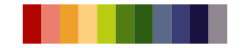

```mathematica
ColorData[10,"Image"]
```

```mathematica
colors=Take[ColorData[10,"ColorList"],numOfConfs];
```

```mathematica
colors=Take[{LightRed,LightGreen,LightBlue,LightOrange,LightBrown,LightCyan,LightMagenta},numOfConfs];
```

ID | SUCCESS %
0A | 99.
.001A | 100.
.005A | 100.
.01A | 100.
.05A | 100.
.1A | 100.
.2A | 100.
.5A | 100.
0B | 91.
.001B | 100.
.005B | 100.
.01B | 100.
.05B | 100.
.1B | 100.
.2B | 100.
.5B | 99.
0C | 100.
.001C | 100.
.005C | 100.
.01C | 100.
.05C | 100.
.1C | 100.
.2C | 100.
.5C | 100.
0D | 100.
.001D | 100.
.005D | 100.
.01D | 100.
.05D | 100.
.1D | 99.
.2D | 100.
.5D | 99.
0E | 93.
.001E | 97.
.005E | 96.
.01E | 95.
.05E | 94.
.1E | 94.
.2E | 88.
.5E | 72.
0F | 90.
.001F | 92.
.005F | 95.
.01F | 93.
.05F | 91.
.1F | 89.
.2F | 83.
.5F | 60.
0G | 85.
.001G | 90.
.005G | 91.
.01G | 90.
.05G | 89.
.1G | 73.
.2G | 65.
.5G | 44.
0H | 51.
.001H | 53.
.005H | 42.
.01H | 39.
.05H | 35.
.1H | 24.
.2H | 20.
.5H | 17.
0I | 3.
.001I | 3.
.005I | 6.
.01I | 4.
.05I | 4.
.1I | 4.
.2I | 0.
.5I | 1.
0J | 49.
.001J | 41.
.005J | 31.
.01J | 33.
.05J | 23.
.1J | 11.
.2J | 21.
.5J | 15.
0K | 3.
.001K | 3.
.005K | 1.
.01K | 1.
.05K | 1.
.1K | 2.
.2K | 1.
.5K | 1.

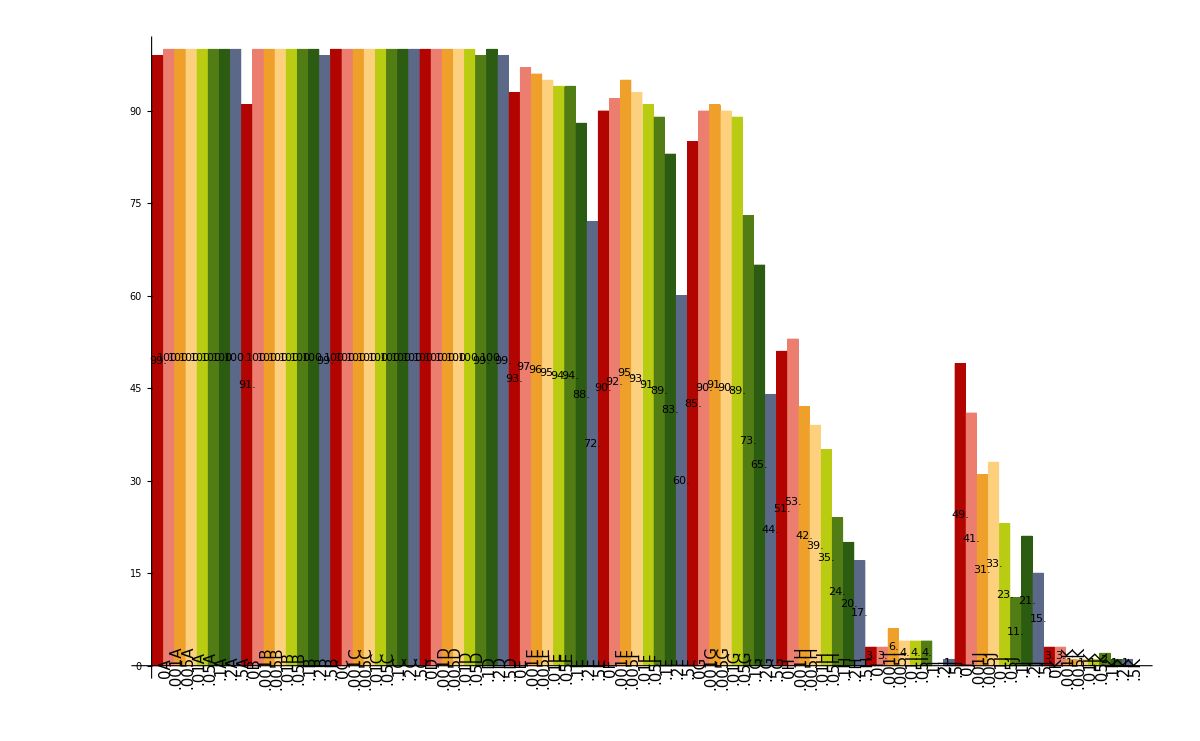

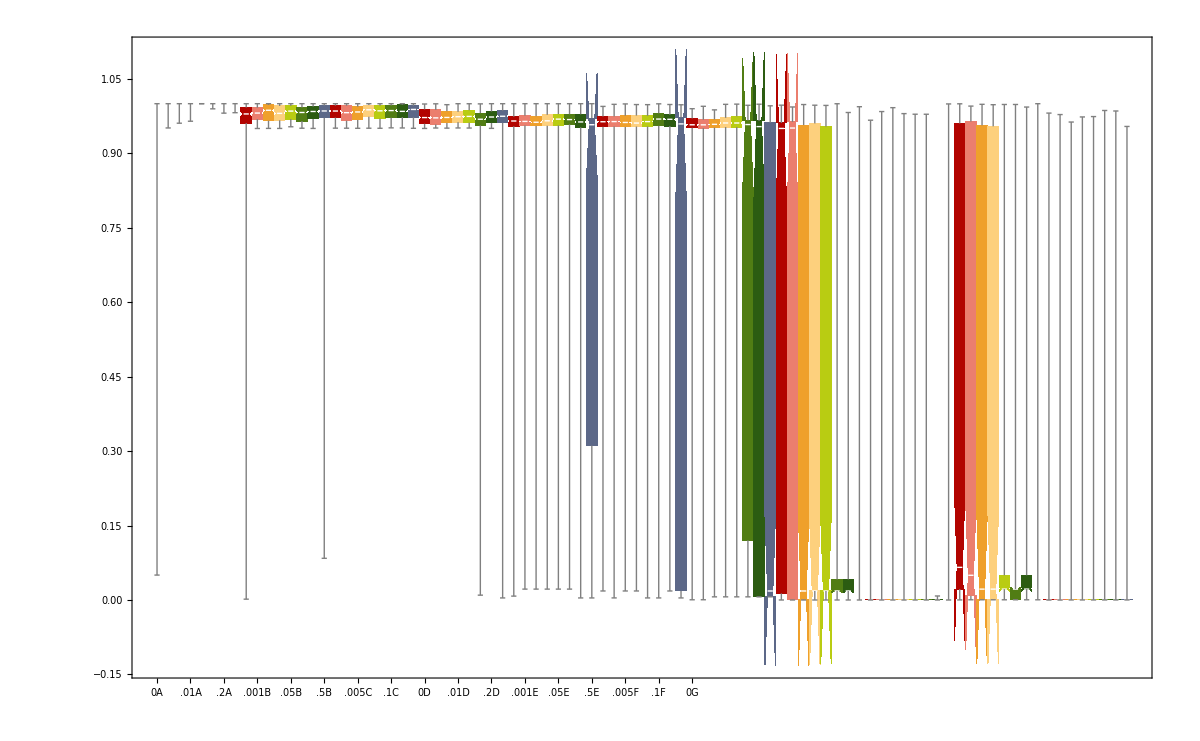
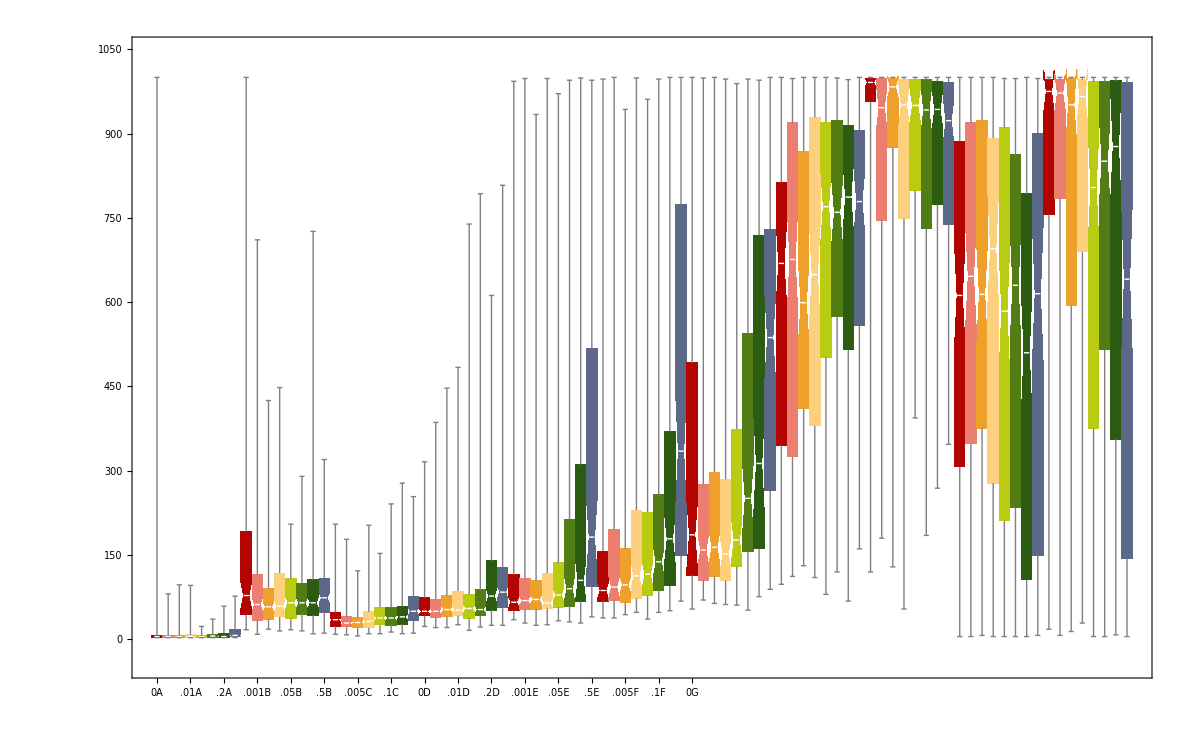
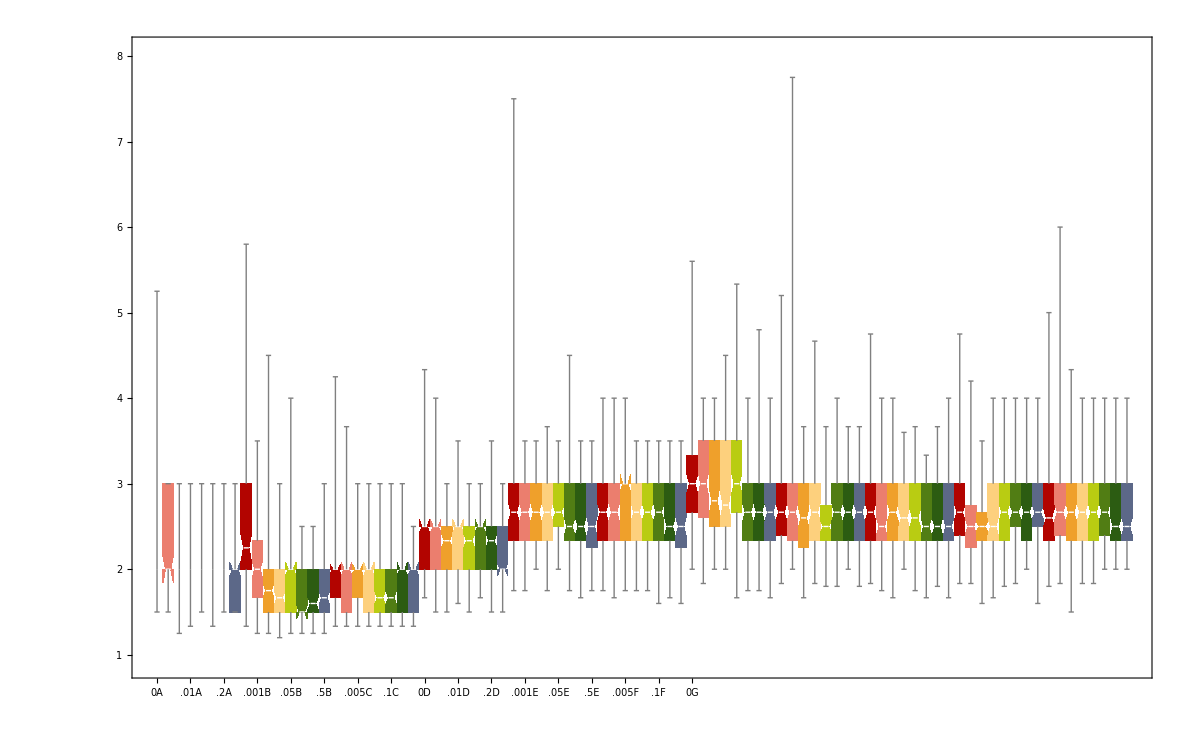
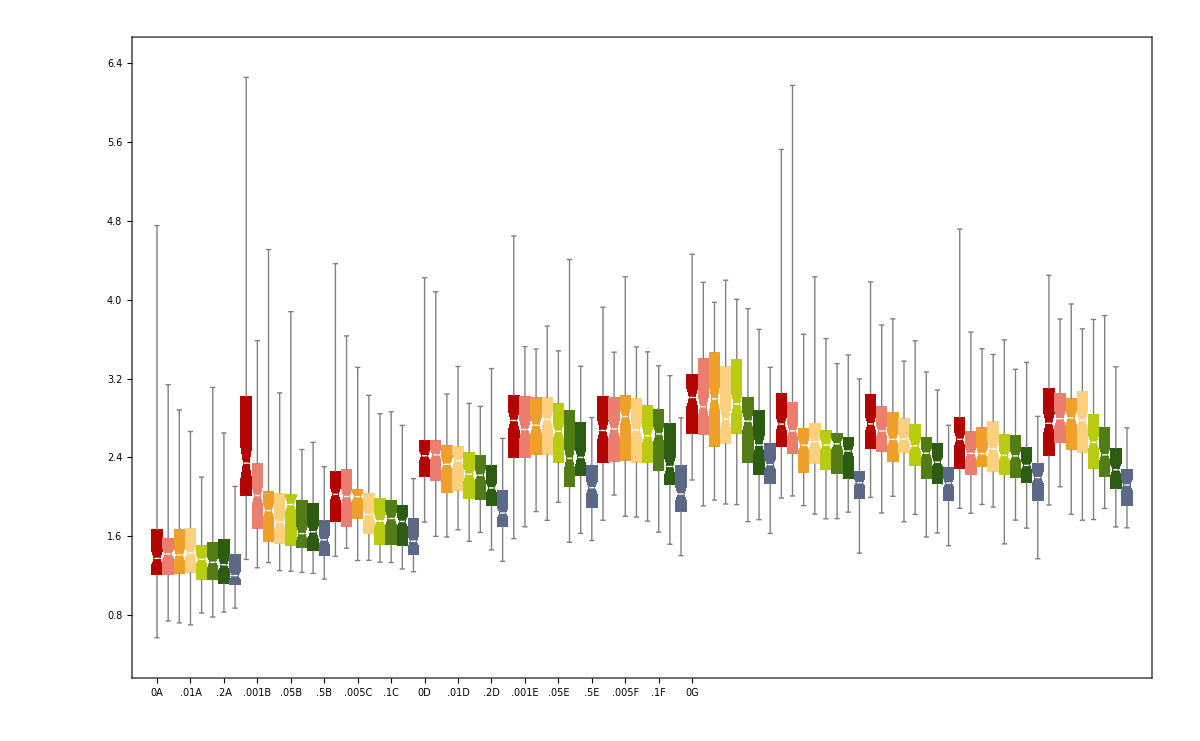
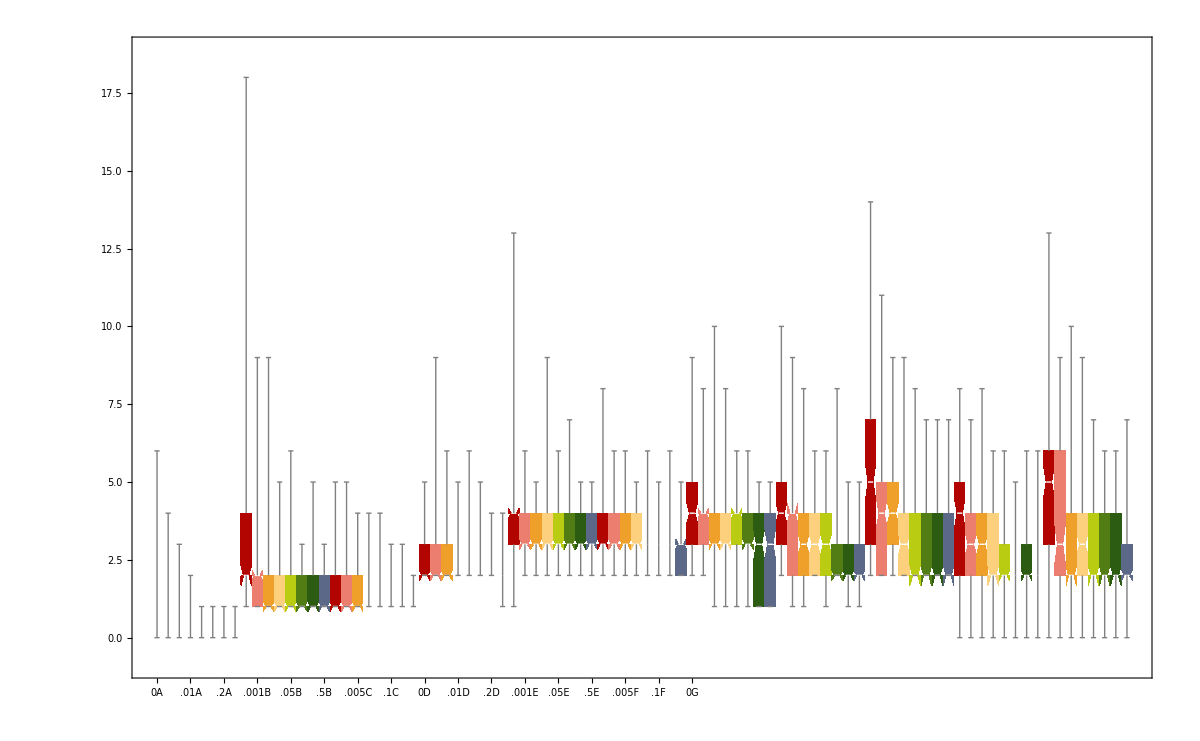
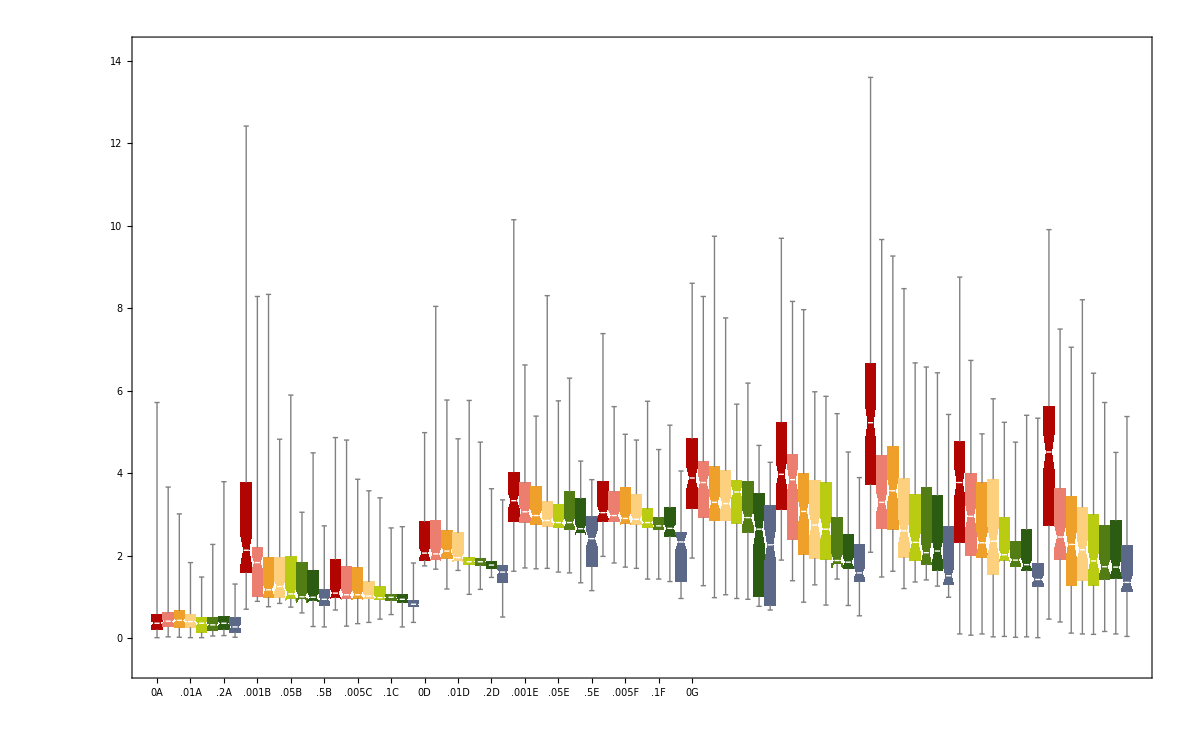
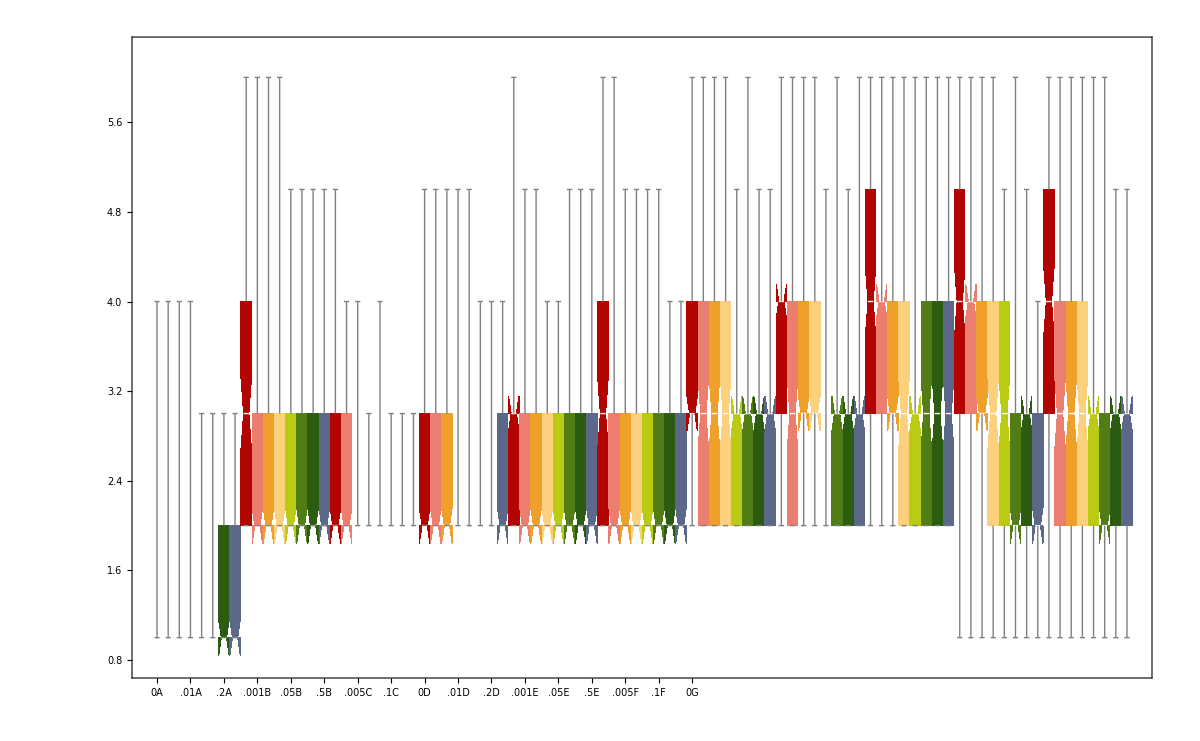
BSF | -Graphics-
BSFG | -Graphics-
ARITY_BSF | -Graphics-
ARITY_LG | -Graphics-
CONSTANTS_BSF | -Graphics-
CONSTANTS_LG | -Graphics-
DEPTH_BSF | -Graphics-
DEPTH_LG | -Graphics-
LEAVES_BSF | -Graphics-
LEAVES_LG | -Graphics-
NODES_BSF | -Graphics-
NODES_LG | -Graphics-
GENERATIONS | -Graphics-
EVALUATIONS | -Graphics-
MAX_FITNESS | -Graphics-
SUCCESS | -Graphics-
TIME | -Graphics-

```mathematica
finalStatsAll[files,labels,Null,colors]
```